```mathematica
(*Load MaTeX so that LaTeX-formatted symbols can be used in axis labels*)
<<MaTeX`
(*We use the experimentally extracted feature line as the reference curve for the polynomial fit.
Figure 6 shows that this feature line follows the measured intensity ridge very well,so it is a suitable target for constructing an analytic fitting function.*)

(*'pic' stores the feature lines*)
pic = -Graphics-;
(*------------------------------------------------------------------*)(*Coordinates of the feature line extracted from the 'pic'.*)

coordinate ={{61.35714285714286,332.7396039072712},{71.,276.3110324786997},{76.,234.88246105012828},{78.5,203.09674676441398},{79.57142857142858,170.95388962155684},{78.85714285714286,141.3110324786997},{76.,107.38246105012826},{69.92857142857144,66.31103247869967},{61.71428571428572,9.168175335842534}};
(*Extract only the y-coordinates.*)
coorY = coordinate⟦1;;,2⟧;
(*Define the sampling points of γ (gamma) on[0,π] with equal spacing of π/8.
These are mapped to the feature-line points above.*)
coorX=Range[0,π,π/8];
(*Combine γ (x) and y into a list of {x,y} pairs for fitting.*)
coor = {coorX,coorY}//Transpose;
(*Store the list of γ values explicitly.*)
γ={0,π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π};
```

### Polynomial Fitting

-1.72825 γ^5+13.6174 γ^4-49.2045 γ^3+96.8621 γ^2-175.559 γ+332.773

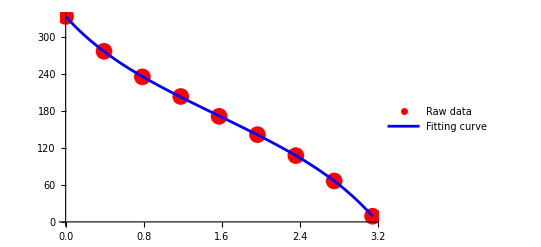

```mathematica
(* ==================================================================*)
(*Polynomial fitting of the feature line*)
(* ==================================================================*)

(*Perform a fifth-order polynomial fit y(x)=a+b x+c x^2+... to the data'coor'.
NonlinearModelFit returns a model object that can be evaluated as y[x] later.*)
y= NonlinearModelFit[coor,a+b x+c x^2+d x^3+e x^4+f x^5,{a,b,c,d,e,f},x];
(*Clear any previous numeric value of γ so that it can be used purely as a symbolic variable or as a list of points again.*)
γ=.
(*Print the explicit polynomial expression in traditional math notation.*)
y[γ]//Normal//TraditionalForm
(*Plot the discrete data and the fitted polynomial on the same axes.*)
Show[
(*Discrete data of the feature line (red dots).*)
ListPlot[coor,PlotStyle->{Red,PointSize[0.03]},PlotLegends->Placed[PointLegend[{Red},{"Raw data"},LegendMarkers->{{"●",15}}   (* ←enlarge marker here*)],Right]],
(*Continuous fifth-order polynomial curve y(x) (blue line).*)
Plot[y[x],{x,0,π},PlotStyle->Blue,PlotLegends->{"Fitting curve"}],
(*Global plot options.*)
Background->White,
LabelStyle->{FontSize->18,FontFamily->"Times",Black,Bold},
(*Axis labels rendered with LaTeX-style bold symbols.*)
AxesLabel->{MaTeX["\\bm{\\gamma}",Magnification->2,Preamble->{"\\usepackage{bm}"}],
MaTeX["\\bm{y}",Magnification->2,Preamble->{"\\usepackage{bm}"}]},
(*Place ticks for γ in degrees from 0° to 360° with a 30° step.*)
Ticks->{Table[i,{i,0,360°,30°}]}
]
```